```mathematica
Manipulate[Plot[x1 Sin[x]+x2 Sin[2x]+x3 Sin[3x]+x8 Sin[8x],{x,0,2π},PlotRange->{-4,4}],{x1,0,1},{x2,0,1},{x3,0,1},{x8,0,1}]
```

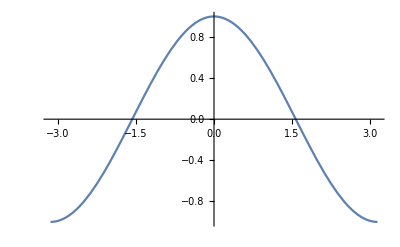

```mathematica
Plot[Cos[x],{x,-π,π}]
```

```mathematica
ⅇ^(i θ)=Cos[θ]+ⅈ Sin[θ]
```

```mathematica
Series[Sin[x],{x,0,10}]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11

```mathematica
Series[Cos[x],{x,0,10}]
```

1-x^2/2+x^4/24-x^6/720+x^8/40320-x^10/3628800+O[x]^11

```mathematica
Series[Exp[x],{x,0,10}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+O[x]^11

```mathematica
Normal[1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+O[x]^11]
```

```mathematica
1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800/.x->ⅈ x
```

```mathematica
FullSimplify[ReIm[1+ⅈ x-x^2/2-(ⅈ x^3)/6+x^4/24+(ⅈ x^5)/120-x^6/720-(ⅈ x^7)/5040+x^8/40320+(ⅈ x^9)/362880-x^10/3628800],x∈Reals]
```

{1-(x^2 (1814400-151200 x^2+5040 x^4-90 x^6+x^8))/3628800,x-x^3/6+x^5/120-x^7/5040+x^9/362880}

```mathematica
r ⅇ^(i θ)
```

```mathematica
ⅇ^(i θ)=Cos[θ]+ⅈ Sin[θ]
```

```mathematica
Expand[(Cos[θ]+ⅈ Sin[θ])(Cos[θ]-ⅈ Sin[θ])]
```

Cos[θ]^2+Sin[θ]^2

```mathematica
{1,2}->1 x̂+2 ŷ
```

```mathematica
{1,2,3,4,5,...}->1Sin[1x]+2Sin[2x]+3Sin[3x]+...
```

```mathematica
bones=;
```

```mathematica
Spectrogram[bones,ImageSize->800,MaxPlotPoints->Infinity,PlotRange->{20,20000}]
```



```mathematica
Plot[Sin[x],{x,0,2π}]
```

```mathematica
Series[Sin[x],{x,0,10}]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11

```mathematica
Manipulate[Column[{Plot[{Sin[x],Evaluate@Normal@Series[Sin[x],{x,0,n}]},{x,-π,π}],Evaluate@Normal@Series[Sin[x],{x,0,n}]}],{n,1,12,1}]
```

```mathematica
{1,2,3,...}
```

```mathematica
{1,0,-1/6,0,1/120,0,-1/5040,0,...}->x+0 x^2-x^3/6+0 x^4+x^5/120+0 x^6-x^7/5040
```

```mathematica
complexData=Partition[RandomComplex[{-1-ⅈ,1+ⅈ},9],3];
```

```mathematica
MatrixForm[complexData]
```

(0.11253+0.353154 ⅈ | -0.962191-0.0479581 ⅈ | 0.799544+0.0633886 ⅈ
-0.249905+0.860177 ⅈ | 0.372507+0.818611 ⅈ | 0.741832+0.6543 ⅈ
-0.483573-0.987748 ⅈ | 0.772905+0.750915 ⅈ | 0.959568-0.837465 ⅈ)

```mathematica
complexData
```

```mathematica
r5=RandomInteger[{1,5},{5,5}];
```

```mathematica
r5//MatrixForm
```

(5 | 2 | 1 | 1 | 5
2 | 4 | 5 | 3 | 1
3 | 2 | 2 | 3 | 5
1 | 4 | 4 | 2 | 2
1 | 5 | 3 | 3 | 1)

```mathematica
Map[f,r5] (*f/@r5*)//MatrixForm
```

(f[{5,2,1,1,5}]
f[{2,4,5,3,1}]
f[{3,2,2,3,5}]
f[{1,4,4,2,2}]
f[{1,5,3,3,1}])

```mathematica
Map[f,r5,{2}] (*f/@r5*)//MatrixForm
```

(f[5] | f[2] | f[1] | f[1] | f[5]
f[2] | f[4] | f[5] | f[3] | f[1]
f[3] | f[2] | f[2] | f[3] | f[5]
f[1] | f[4] | f[4] | f[2] | f[2]
f[1] | f[5] | f[3] | f[3] | f[1])

```mathematica
Abs[RandomComplex[{-1-ⅈ,1+ⅈ}]]
```

0.664258

```mathematica
RandomComplex[{-1-ⅈ,1+ⅈ}]
```

```mathematica
FullForm[0.579443+0.8246679479099379 ⅈ]
```

Complex[0.579443,0.824668]

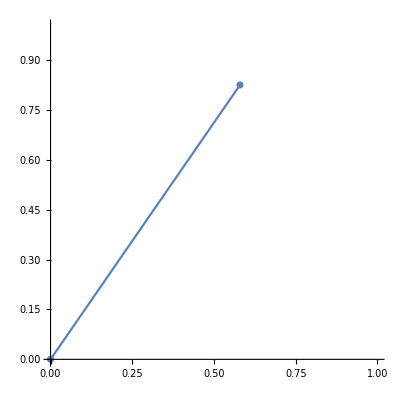

```mathematica
ListPlot[{{0,0},{0.579443,0.8246679479099379}},Joined->True,Mesh->All,AspectRatio->1,PlotRange->{{0,1},{0,1}}]
```

```mathematica
abs[complex]=Re[complex]^2+Im[complex]^2
phase[complex]=ArcTan[Im[complex]/Re[complex]]
```

```mathematica
complexData//MatrixForm
```

(0.11253+0.353154 ⅈ | -0.962191-0.0479581 ⅈ | 0.799544+0.0633886 ⅈ
-0.249905+0.860177 ⅈ | 0.372507+0.818611 ⅈ | 0.741832+0.6543 ⅈ
-0.483573-0.987748 ⅈ | 0.772905+0.750915 ⅈ | 0.959568-0.837465 ⅈ)

```mathematica
magPhaseData=Map[{Abs[#],ArcTan[Im[#]/Re[#]]}&,complexData,{2}];
```

```mathematica
magPhaseData//MatrixForm
```

((0.370649
1.26232) | (0.963385
0.0498014) | (0.802053
0.0791154)
(0.895744
-1.28805) | (0.899381
1.14375) | (0.989153
0.722784)
(1.09977
1.11553) | (1.07762
0.770969) | (1.27362
-0.717556))

```mathematica
r ⅇ^(ⅈ phase)
```

```mathematica
Map[#[[1]]Exp[ⅈ #[[2]]]&,magPhaseData,{2}]//MatrixForm
```

(0.11253+0.353154 ⅈ | 0.962191+0.0479581 ⅈ | 0.799544+0.0633886 ⅈ
0.249905-0.860177 ⅈ | 0.372507+0.818611 ⅈ | 0.741832+0.6543 ⅈ
0.483573+0.987748 ⅈ | 0.772905+0.750915 ⅈ | 0.959568-0.837465 ⅈ)

```mathematica
complexData//MatrixForm
```

(0.11253+0.353154 ⅈ | -0.962191-0.0479581 ⅈ | 0.799544+0.0633886 ⅈ
-0.249905+0.860177 ⅈ | 0.372507+0.818611 ⅈ | 0.741832+0.6543 ⅈ
-0.483573-0.987748 ⅈ | 0.772905+0.750915 ⅈ | 0.959568-0.837465 ⅈ)

```mathematica
stfData=FullForm[ShortTimeFourier[bones]][[1,1,"Data"]];
```

```mathematica
stfData[[;;3,;;3]]//MatrixForm
```

(0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ)

```mathematica
MatrixPlot[Abs[stfData]]
```

```mathematica
stfData[[1000;;1005,2000;;2005]]//MatrixForm
```

(-0.238473+0.0100054 ⅈ | -0.238478+0.00979396 ⅈ | -0.238463+0.00961764 ⅈ | -0.238533+0.0093595 ⅈ | -0.23847+0.00920324 ⅈ | -0.238492+0.00896409 ⅈ
0.929996-0.0364857 ⅈ | 0.929947-0.0356755 ⅈ | 0.929932-0.0349951 ⅈ | 0.929949-0.0343201 ⅈ | 0.929911-0.0335048 ⅈ | 0.92989-0.0327846 ⅈ
0.349435-0.0123726 ⅈ | 0.349406-0.012186 ⅈ | 0.349373-0.0118641 ⅈ | 0.349427-0.0116551 ⅈ | 0.349379-0.0114158 ⅈ | 0.34936-0.0111458 ⅈ
0.786197-0.0282954 ⅈ | 0.786168-0.0277231 ⅈ | 0.786207-0.0271475 ⅈ | 0.786186-0.026564 ⅈ | 0.786164-0.0260406 ⅈ | 0.78619-0.0254475 ⅈ
-0.110744+0.00582731 ⅈ | -0.11072+0.00569589 ⅈ | -0.110754+0.00558772 ⅈ | -0.110823+0.00544864 ⅈ | -0.110754+0.00532739 ⅈ | -0.11078+0.00520103 ⅈ
0.0213751-0.000530367 ⅈ | 0.0213384-0.000490605 ⅈ | 0.021373-0.000490353 ⅈ | 0.0213429-0.000522346 ⅈ | 0.0213273-0.000461176 ⅈ | 0.0213594-0.0004635 ⅈ)

```mathematica
Abs@stfData[[1000;;1005,2000;;2005]]//MatrixForm
```

(0.238683 | 0.238679 | 0.238657 | 0.238717 | 0.238648 | 0.23866
0.930712 | 0.930631 | 0.93059 | 0.930582 | 0.930514 | 0.930468
0.349654 | 0.349618 | 0.349574 | 0.349622 | 0.349566 | 0.349538
0.786706 | 0.786657 | 0.786675 | 0.786635 | 0.786595 | 0.786602
0.110897 | 0.110866 | 0.110895 | 0.110957 | 0.110882 | 0.110902
0.0213817 | 0.0213441 | 0.0213787 | 0.0213493 | 0.0213323 | 0.0213644)

```mathematica
Map[ArcTan[Im[#]/Re[#]]&,stfData[[1000;;1005,2000;;2005]],{2}]//MatrixForm
```

(-0.0419315 | -0.0410456 | -0.0403099 | -0.0392177 | -0.0385737 | -0.0375689
-0.039212 | -0.0383442 | -0.0376142 | -0.0368886 | -0.0360145 | -0.0352419
-0.0353927 | -0.0348621 | -0.0339453 | -0.0333424 | -0.0326628 | -0.0318926
-0.0359747 | -0.0352489 | -0.034516 | -0.0337756 | -0.0331115 | -0.0323568
-0.0525713 | -0.0513988 | -0.0504087 | -0.0491257 | -0.0480642 | -0.0469147
-0.0248072 | -0.0229876 | -0.0229386 | -0.0244691 | -0.0216203 | -0.0216967)

```mathematica
MapAt[0*#&,Map[ArcTan[Im[#]/Re[#]]&,stfData[[1000;;1005,2000;;2005]],{2}],{All,3}]//MatrixForm
```

(-0.0419315 | -0.0410456 | 0. | -0.0392177 | -0.0385737 | -0.0375689
-0.039212 | -0.0383442 | 0. | -0.0368886 | -0.0360145 | -0.0352419
-0.0353927 | -0.0348621 | 0. | -0.0333424 | -0.0326628 | -0.0318926
-0.0359747 | -0.0352489 | 0. | -0.0337756 | -0.0331115 | -0.0323568
-0.0525713 | -0.0513988 | 0. | -0.0491257 | -0.0480642 | -0.0469147
-0.0248072 | -0.0229876 | 0. | -0.0244691 | -0.0216203 | -0.0216967)

```mathematica
Audio[InverseShortTimeFourier[MapAt[0*#&,stfData,300;;350]]]
```

```mathematica
Spectrogram[,ImageSize->800,MaxPlotPoints->Infinity,PlotRange->{20,20000}]
```

```mathematica
Dimensions@stfData
```

{5553,4096}

```mathematica
{300,350}/5553 Duration[bones]
```

{0 9.28469,0 10.8321}